## Introduction

Chimeras states in swarmalators on a 1D. See paper for definition of model. Found four states:

1. Regular chimera: with space dynamics turned off J = 0
2. Shy chimera: a clusters of sync’d swarmalatoes (head of chimera) co-exists with a traveling / metachronal wave (tail of chimera). Dynamic state; the head periodically hides behind the tail as if the chimera is “shy”. This states need more investigation.
3. Snake state: an S-shaped shape that wriggles like snake. Believe this is bistable with the sync wave. For small N, it looks to be stable. For large N, it looks to be a saddle that it periodically approached and repelled.
4. Sync wave: swamaltors are uniform in space and fully in sync

If we could do some analysis on the snake state and ideally the shy chimera we could get into PRL.

Note the following coordinates are useful

ξ = x+θ
η = x - θ

#### Papers

These states look to match the behavior of vinegar eels: see paper below.

“Synchronized oscillations in swarms of nematode Turbatrix aceti”

Pipe flow: turbluence.

Turbulence in a population of swarmalators

#### Photo of states

```mathematica
fig=Import["Desktop/states.png"]
```

Import::nffil: File Desktop/states.png not found during Import.

$Failed

## Main

### Simulate with movie (real time updates)

```mathematica
SeedRandom[0];
{dt,T,n1}={0.5,2000,100}; 
(*{J,k,β}={0,1,0.1};*)  (*Regular chimera*)
(*{J,k,β}={-0.1,1,0.1};  (*Shy chimera*)*)
{J,k,β}={-0.4,1,0.1};  (*Snake state*)
(*{J,k,β}={-0.8,1,0.1};*)  (*Sync wave*)
{A,α}={1,π/2-β};
{z0,znew}={{Table[(2π)/n1 i//N,{i,1,n1}],Table[RandomReal[{0,2π}],{i,1,n1}]},ConstantArray[0,{2,n1}]};
results1={};
Dynamic[results1]
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Sps,Sms,Rs,Qs}={{},{},{},{}};
While[t<NT,
znew=rk4New[z0,rhsNew,dt,J,k,A,α];
z0=znew;t++;
{Sp,Sm}=findWs[znew]//Abs;
{Q,R}=findRs[znew]//Abs;
AppendTo[Sps,Sp];AppendTo[Sms,Sm];AppendTo[Rs,R];AppendTo[Qs,Q];
results1=plotResults1D[znew]
]
```

$Aborted

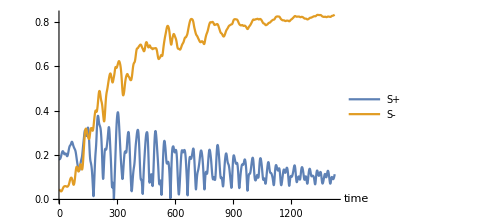
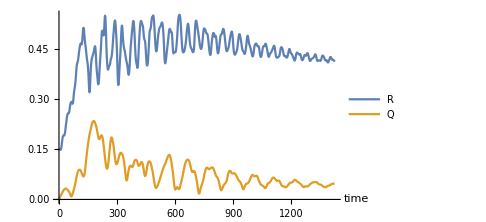
-Graphics- | -Graphics-

```mathematica
p1=ListPlot[{Sps,Sms},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"S+","S-"},Joined->True,ImageSize->Medium,PlotRange->All];
p2=ListPlot[{Rs,Qs},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"R","Q"},Joined->True,ImageSize->Medium,PlotRange->All];
Grid[{{p1,p2}}]
```

#### Aside

```mathematica
{dt,T,n1}={0.5,1000,100};  (*dt = timestep, n = number of swarmalators*)
{J,k,β}={-0.4,1,0.1};      (*Change these parameters to experiment with the swarmalator system*)
{A,α}={1,π/2-β};
{z0,znew}={{Table[(2π)/n1 i//N,{i,1,n1}],Table[RandomReal[{0,2π}],{i,1,n1}]},ConstantArray[0,{2,n1}]};
results1={};
Dynamic[results1]
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Sps,Sms,Rs,Qs}={{},{},{},{}};
While[t<NT,
znew=rk4New[z0,rhsNew,dt,J,k,A,α];
z0=znew;t++;
{Sp,Sm}=findWs[znew]//Abs;
{Q,R}=findRs[znew]//Abs;
AppendTo[Sps,Sp];AppendTo[Sms,Sm];AppendTo[Rs,R];AppendTo[Qs,Q];
results1=plotResults1D[znew]
]
```

$Aborted

### Simulate with no movie (faster)

#### Regular chimera (J, β)=(0,0.1)

As N→∞ the oscillation is the order parameters die out.

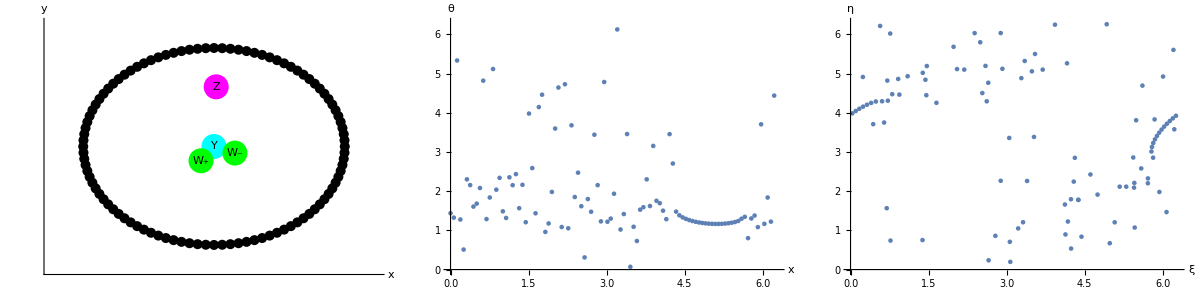

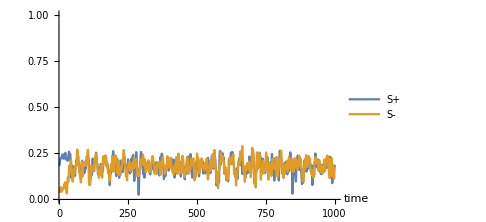
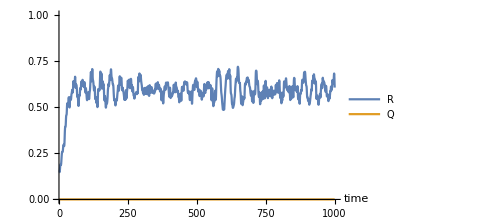
-Graphics- | -Graphics-

```mathematica
(*Simulate*)
SeedRandom[0];
{dt,T,n1}={0.5,1000,100};  (*dt = timestep, n = number of swarmalators*)
{J,k,β}={0,1,0.1};      (*Change these parameters to experiment with the swarmalator system*)
{A,α}={1,π/2-β};
{z0,znew}={{Table[(2π)/n1 i//N,{i,1,n1}],Table[RandomReal[{0,2π}],{i,1,n1}]},ConstantArray[0,{2,n1}]};
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms,Zs,Ys,ts}={{},{},{},{},{}};
While[t<NT,
znew=rk4New[z0,rhsNew,dt,J,k,A,α];
z0=znew;t++;
{Wp,Wm}=findWs[znew];
{Y,Z}=findRs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Zs,Z];AppendTo[Ys,Y];AppendTo[ts,t*dt];
];

(*Plot*)
plotResults1D[znew]
p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"S+","S-"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p2=ListPlot[{{ts,Zs//Abs}ᵀ,{ts,Ys//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"R","Q"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
Grid[{{p1,p2}}]
```

#### Shy chimera (J, β)=(-0.05,0.1)

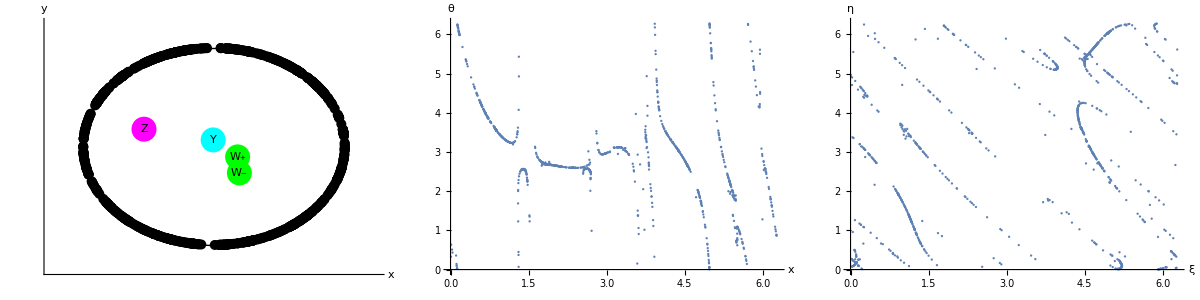

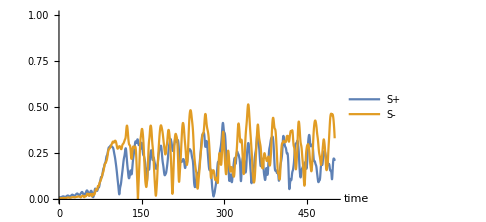
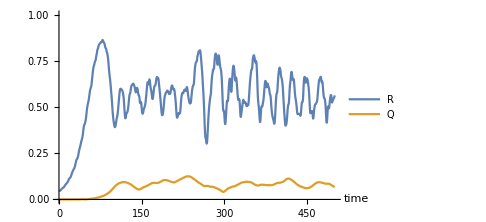
-Graphics- | -Graphics-

```mathematica
(*Simulate*)
SeedRandom[0];
{dt,T,n1}={0.1,500,1000};  (*dt = timestep, n = number of swarmalators*)
{J,k,β}={-0.05,1,0.1};      (*Change these parameters to experiment with the swarmalator system*)
{A,α}={1,π/2-β};
{z0,znew}={{Table[(2π)/n1 i//N,{i,1,n1}],Table[RandomReal[{0,2π}],{i,1,n1}]},ConstantArray[0,{2,n1}]};
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms,Zs,Ys,ts}={{},{},{},{},{}};
While[t<NT,
znew=rk4New[z0,rhsNew,dt,J,k,A,α];
z0=znew;t++;
{Wp,Wm}=findWs[znew];
{Y,Z}=findRs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Zs,Z];AppendTo[Ys,Y];AppendTo[ts,t*dt];
];

(*Plot*)
plotResults1D[znew]
p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"S+","S-"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p2=ListPlot[{{ts,Zs//Abs}ᵀ,{ts,Ys//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"R","Q"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
Grid[{{p1,p2}}]
```

Looks like R and S = max(S+, S-) are anti-correlated.

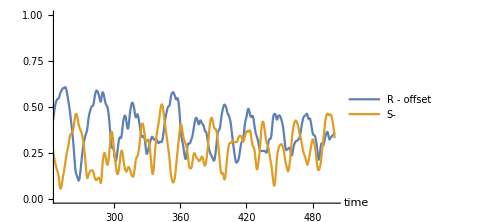

```mathematica
p1=ListPlot[{{ts,Abs[Zs]-0.2}ᵀ,{ts,Wms//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"R - offset","S-"},Joined->True,ImageSize->Medium,PlotRange->{{250,500},{0,1}}]
```

1. Yes.
2. Guess:  when R peaks the head of the chimera dominates, and when S peaks the tail dominates.

#### Snake state (J, β)=(-0.4,0.1)

I believe this state is a saddle: if you run for larger (N, T) we see breathing in the order parameters.
I also believe its bistable with the sync wave. More info to come.
Also, the order parameters always have some oscillations.

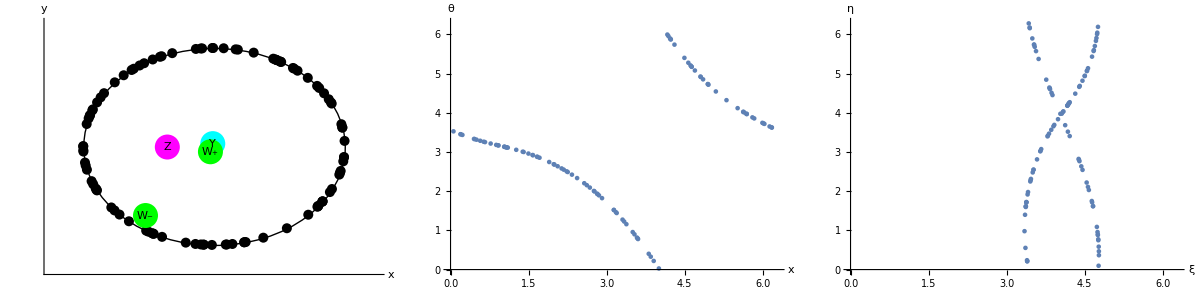

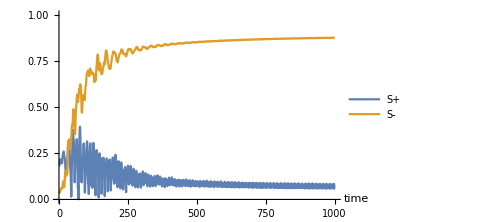
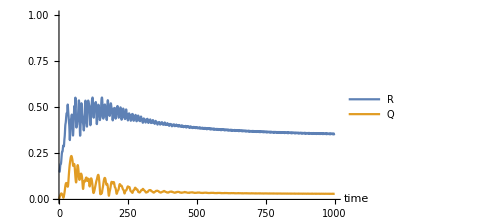
-Graphics- | -Graphics-

```mathematica
(*Simulate*)
SeedRandom[0];
{dt,T,n1}={0.5,1000,100};  (*dt = timestep, n = number of swarmalators*)
{J,k,β}={-0.4,1,0.1};      (*Change these parameters to experiment with the swarmalator system*)
{A,α}={1,π/2-β};
{z0,znew}={{Table[(2π)/n1 i//N,{i,1,n1}],Table[RandomReal[{0,2π}],{i,1,n1}]},ConstantArray[0,{2,n1}]};
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms,Zs,Ys,ts}={{},{},{},{},{}};
While[t<NT,
znew=rk4New[z0,rhsNew,dt,J,k,A,α];
z0=znew;t++;
{Wp,Wm}=findWs[znew];
{Y,Z}=findRs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Zs,Z];AppendTo[Ys,Y];AppendTo[ts,t*dt];
];

(*Plot*)
plotResults1D[znew]
p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"S+","S-"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p2=ListPlot[{{ts,Zs//Abs}ᵀ,{ts,Ys//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"R","Q"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
Grid[{{p1,p2}}]
```

#### Sync wave (J, β)=(-0.6, 0.1)

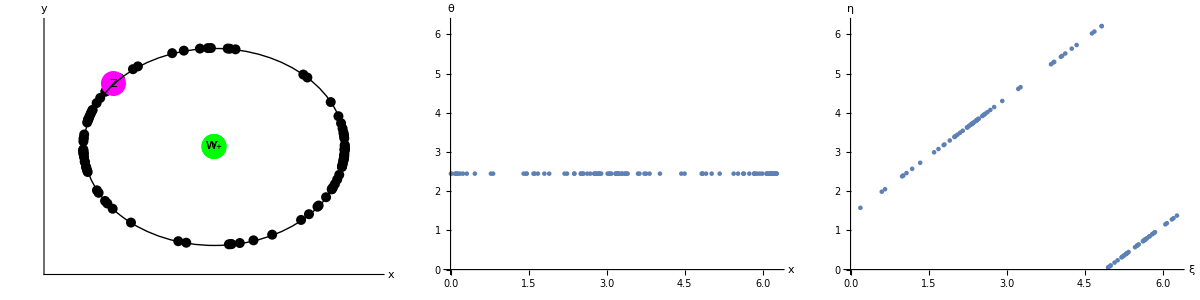

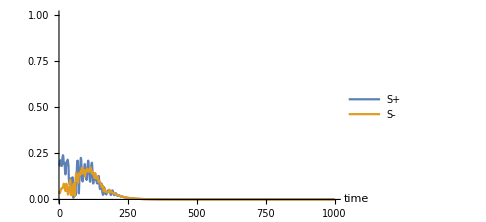
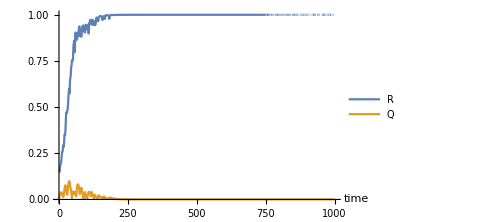
-Graphics- | -Graphics-

```mathematica
(*Simulate*)
SeedRandom[0];
{dt,T,n1}={0.5,1000,100};  (*dt = timestep, n = number of swarmalators*)
{J,k,β}={-0.6,1,0.1};      (*Change these parameters to experiment with the swarmalator system*)
{A,α}={1,π/2-β};
{z0,znew}={{Table[(2π)/n1 i//N,{i,1,n1}],Table[RandomReal[{0,2π}],{i,1,n1}]},ConstantArray[0,{2,n1}]};
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms,Zs,Ys,ts}={{},{},{},{},{}};
While[t<NT,
znew=rk4New[z0,rhsNew,dt,J,k,A,α];
z0=znew;t++;
{Wp,Wm}=findWs[znew];
{Y,Z}=findRs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Zs,Z];AppendTo[Ys,Y];AppendTo[ts,t*dt];
];

(*Plot*)
plotResults1D[znew]
p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"S+","S-"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p2=ListPlot[{{ts,Zs//Abs}ᵀ,{ts,Ys//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"R","Q"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
Grid[{{p1,p2}}]
```

### Aside

$Aborted

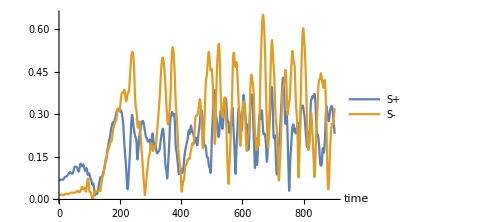
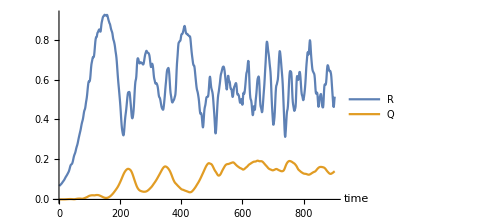
-Graphics- | -Graphics-

```mathematica
SeedRandom[0];
{dt,T,n1}={0.5,2000,500}; 
(*{J,k,β}={0,1,0.1};*)  (*Regular chimera*)
{J,k,β}={-0.1,1,0.1}; (*Shy chimera*)
(*{J,k,β}={-0.4,1,0.1};*)  (*Snake state*)
(*{J,k,β}={-0.8,1,0.1};*)  (*Sync wave*)
{A,α}={1,π/2-β};
{z0,znew}={{Table[(2π)/n1 i//N,{i,1,n1}],Table[RandomReal[{0,2π}],{i,1,n1}]},ConstantArray[0,{2,n1}]};
results1={};
Dynamic[results1]
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Sps,Sms,Rs,Qs}={{},{},{},{}};
While[t<NT,
znew=rk4New[z0,rhsNew,dt,J,k,A,α];
z0=znew;t++;
{Sp,Sm}=findWs[znew]//Abs;
{Q,R}=findRs[znew]//Abs;
AppendTo[Sps,Sp];AppendTo[Sms,Sm];AppendTo[Rs,R];AppendTo[Qs,Q];
results1=plotResults1D[znew]
]
p1=ListPlot[{Sps,Sms},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"S+","S-"},Joined->True,ImageSize->Medium,PlotRange->All];
p2=ListPlot[{Rs,Qs},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"R","Q"},Joined->True,ImageSize->Medium,PlotRange->All];
Grid[{{p1,p2}}]
```

## Snake state stable for small N?

### (N, T) = (100, 5000)

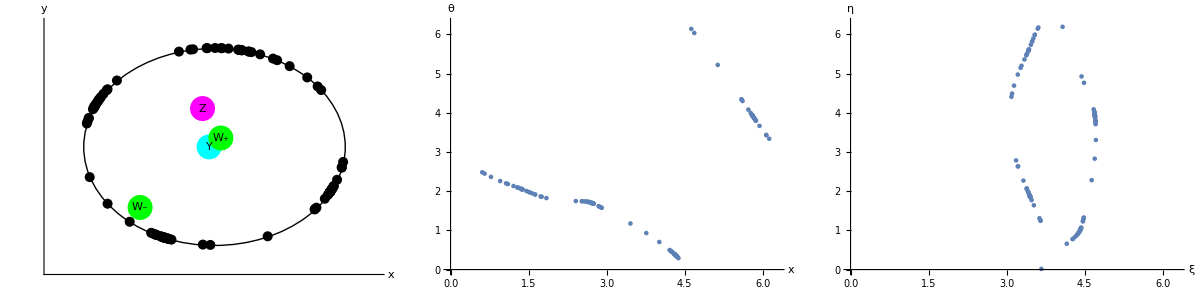

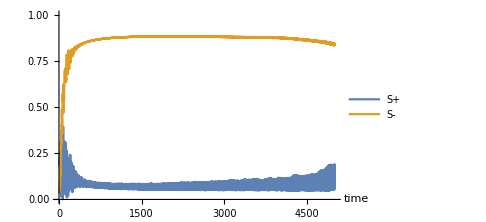
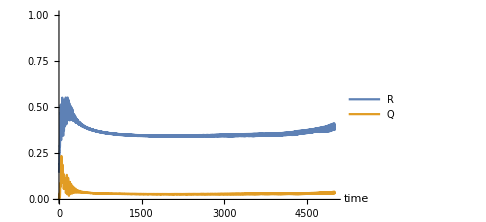
-Graphics- | -Graphics-

```mathematica
(*Simulate*)
SeedRandom[0];
{dt,T,n1}={0.5,5000,100};  (*dt = timestep, n = number of swarmalators*)
{J,k,β}={-0.4,1,0.1};      (*Change these parameters to experiment with the swarmalator system*)
{A,α}={1,π/2-β};
{z0,znew}={{Table[(2π)/n1 i//N,{i,1,n1}],Table[RandomReal[{0,2π}],{i,1,n1}]},ConstantArray[0,{2,n1}]};
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms,Zs,Ys,ts}={{},{},{},{},{}};
While[t<NT,
znew=rk4New[z0,rhsNew,dt,J,k,A,α];
z0=znew;t++;
{Wp,Wm}=findWs[znew];
{Y,Z}=findRs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Zs,Z];AppendTo[Ys,Y];AppendTo[ts,t*dt];
];

(*Plot*)
plotResults1D[znew]
p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"S+","S-"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p2=ListPlot[{{ts,Zs//Abs}ᵀ,{ts,Ys//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"R","Q"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
Grid[{{p1,p2}}]
```

### (N, T) = (100, 20000)

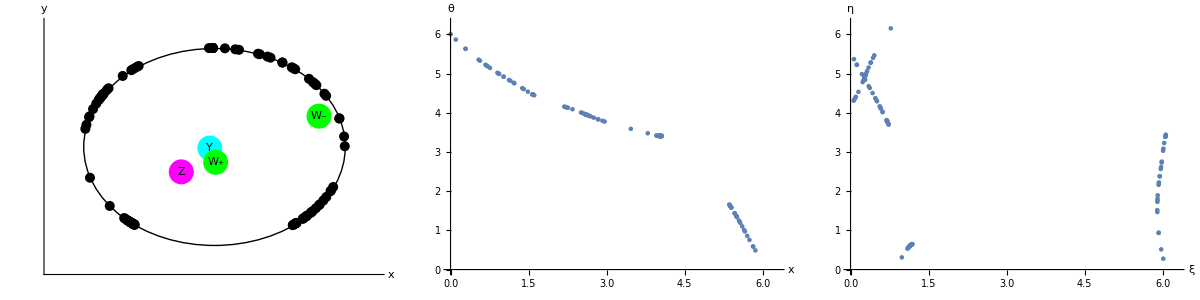

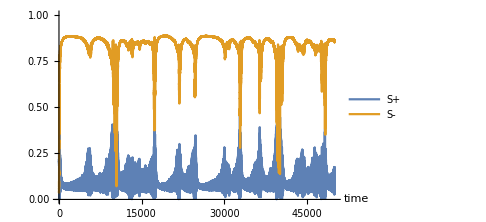
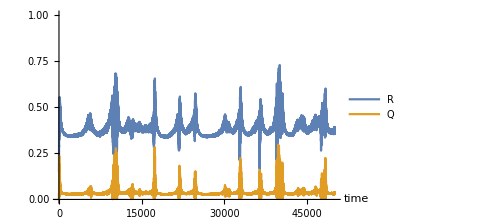
-Graphics- | -Graphics-

```mathematica
(*Simulate*)
SeedRandom[0];
{dt,T,n1}={0.5,50000,100};  (*dt = timestep, n = number of swarmalators*)
{J,k,β}={-0.4,1,0.1};      (*Change these parameters to experiment with the swarmalator system*)
{A,α}={1,π/2-β};
{z0,znew}={{Table[(2π)/n1 i//N,{i,1,n1}],Table[RandomReal[{0,2π}],{i,1,n1}]},ConstantArray[0,{2,n1}]};
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms,Zs,Ys,ts}={{},{},{},{},{}};
While[t<NT,
znew=rk4New[z0,rhsNew,dt,J,k,A,α];
z0=znew;t++;
{Wp,Wm}=findWs[znew];
{Y,Z}=findRs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Zs,Z];AppendTo[Ys,Y];AppendTo[ts,t*dt];
];

(*Plot*)
plotResults1D[znew]
p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"S+","S-"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p2=ListPlot[{{ts,Zs//Abs}ᵀ,{ts,Ys//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"R","Q"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
Grid[{{p1,p2}}]
```

### (N, T) = (500, 10000)

$Aborted

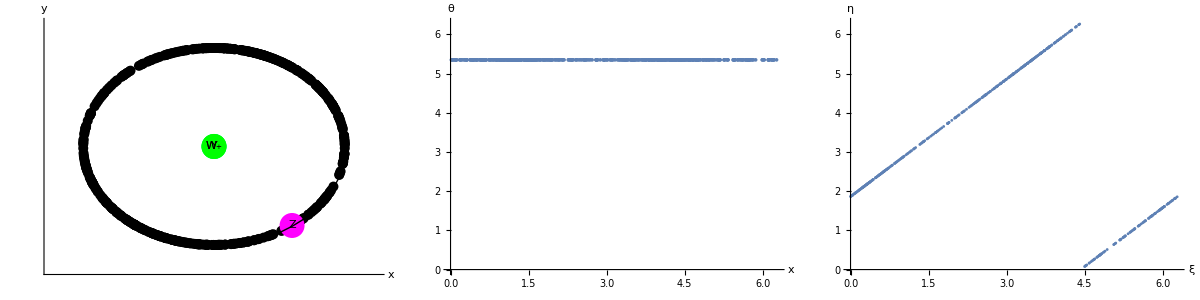

$Aborted

$Aborted

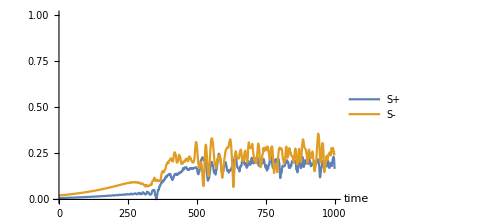
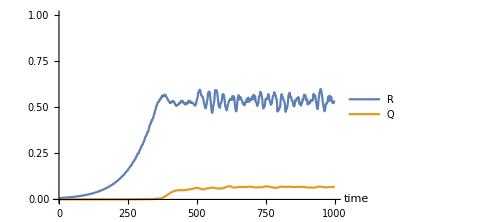
-Graphics- | -Graphics-

```mathematica
(*Simulate*)
SeedRandom[0];
{dt,T,n1}={0.5,10000,500};  (*dt = timestep, n = number of swarmalators*)
{J,k,β}={-0.4,1,0.1};      (*Change these parameters to experiment with the swarmalator system*)
{A,α}={1,π/2-β};
{z0,znew}={{Table[(2π)/n1 i//N,{i,1,n1}],Table[RandomReal[{0,2π}],{i,1,n1}]},ConstantArray[0,{2,n1}]};
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms,Zs,Ys,ts}={{},{},{},{},{}};
While[t<NT,
znew=rk4New[z0,rhsNew,dt,J,k,A,α];
z0=znew;t++;
{Wp,Wm}=findWs[znew];
{Y,Z}=findRs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Zs,Z];AppendTo[Ys,Y];AppendTo[ts,t*dt];
];

(*Plot*)
plotResults1D[znew]
p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"S+","S-"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p2=ListPlot[{{ts,Zs//Abs}ᵀ,{ts,Ys//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"R","Q"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
Grid[{{p1,p2}}]
```

## Snake state bistable with sync wave

### Snake state: N = 500

#### Start from R = 0 (uniform)

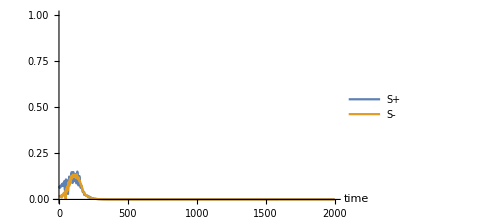
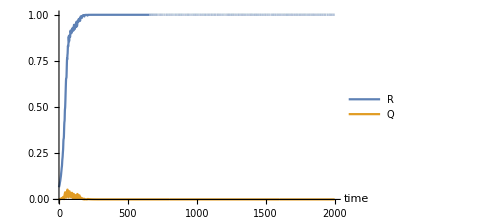
-Graphics- | -Graphics-

```mathematica
SeedRandom[0];
{dt,T,n1}={0.1,2000,500};  (*dt = timestep, n = number of swarmalators*)
{J,k,β}={-0.5,1,0.1};      (*Change these parameters to experiment with the swarmalator system*)
{A,α}={1,π/2-β};
{z0,znew}={{Table[(2π)/n1 i//N,{i,1,n1}],Table[RandomReal[{0,2π}],{i,1,n1}]},ConstantArray[0,{2,n1}]};
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms,Zs,Ys,ts}={{},{},{},{},{}};
While[t<NT,
znew=rk4New[z0,rhsNew,dt,J,k,A,α];
z0=znew;t++;
{Wp,Wm}=findWs[znew];
{Y,Z}=findRs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Zs,Z];AppendTo[Ys,Y];AppendTo[ts,t*dt];
];
p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"S+","S-"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p2=ListPlot[{{ts,Zs//Abs}ᵀ,{ts,Ys//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"R","Q"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
Grid[{{p1,p2}}]
```

#### Start from R = 1 (sync)

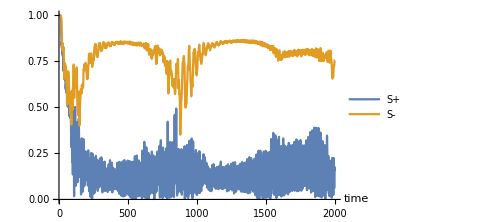
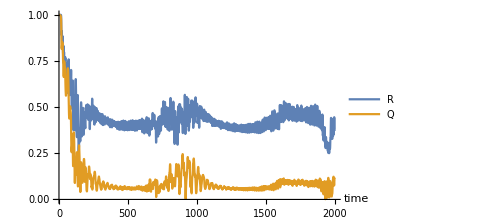
-Graphics- | -Graphics-

```mathematica
SeedRandom[0];
{dt,T,n1}={0.1,2000,500};  (*dt = timestep, n = number of swarmalators*)
{J,k,β}={-0.5,1,0.1};      (*Change these parameters to experiment with the swarmalator system*)
{A,α}={1,π/2-β};
{z0,znew}={{Table[RandomReal[{0,0.1}],{i,1,n1}],Table[RandomReal[{0,0.1}],{i,1,n1}]},ConstantArray[0,{2,n1}]};
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps1,Wms1,Zs1,Ys1,ts}={{},{},{},{},{}};
While[t<NT,
znew=rk4New[z0,rhsNew,dt,J,k,A,α];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
{Y1,Z1}=findRs[znew];
AppendTo[Wps1,Wp1];AppendTo[Wms1,Wm1];AppendTo[Zs1,Z1];AppendTo[Ys1,Y1];AppendTo[ts,t*dt];
];
p1=ListPlot[{{ts,Wps1//Abs}ᵀ,{ts,Wms1//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"S+","S-"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p2=ListPlot[{{ts,Zs1//Abs}ᵀ,{ts,Ys1//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"R","Q"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
Grid[{{p1,p2}}]
```

#### Plot together

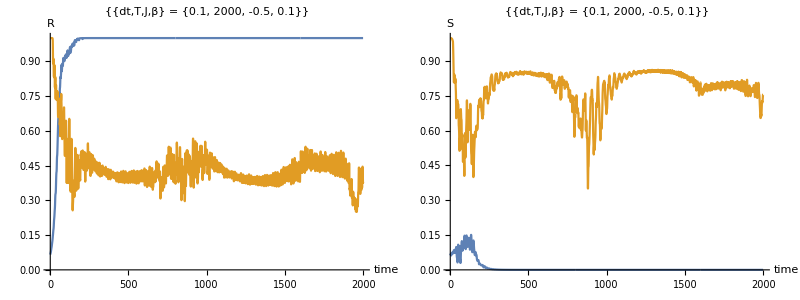

```mathematica
p1=ListPlot[{{ts,Zs//Abs}ᵀ,{ts,Zs1//Abs}ᵀ},AxesOrigin->{0,0},ImageSize->Medium,AxesLabel->{Style["time",15],Style["R",15]},Joined->True,ImageSize->Medium PlotRange->{0,1},PlotLabel->{"{dt,T,J,β} = "<>ToString[{dt,T,J,β}]}];
p2=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms1//Abs}ᵀ},ImageSize->Medium,AxesOrigin->{0,0},AxesLabel->{Style["time",15],Style["S",15]},Joined->True,ImageSize->Medium PlotRange->{0,1},PlotLabel->{"{dt,T,J,β} = "<>ToString[{dt,T,J,β}]}];
Grid[{{p1,p2}}]
```

### Snake state: N = 1000 (check for convergence)

#### Start from R = 0 (uniform)

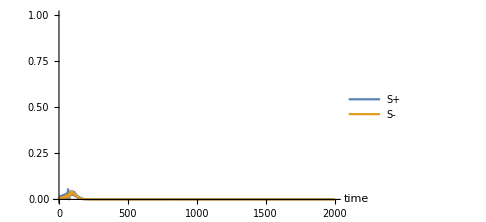
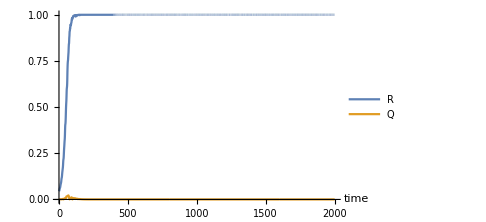
-Graphics- | -Graphics-

```mathematica
SeedRandom[0];
{dt,T,n1}={0.1,2000,1000};  (*dt = timestep, n = number of swarmalators*)
{J,k,β}={-0.5,1,0.1};      (*Change these parameters to experiment with the swarmalator system*)
{A,α}={1,π/2-β};
{z0,znew}={{Table[(2π)/n1 i//N,{i,1,n1}],Table[RandomReal[{0,2π}],{i,1,n1}]},ConstantArray[0,{2,n1}]};
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms,Zs,Ys,ts}={{},{},{},{},{}};
While[t<NT,
znew=rk4New[z0,rhsNew,dt,J,k,A,α];
z0=znew;t++;
{Wp,Wm}=findWs[znew];
{Y,Z}=findRs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Zs,Z];AppendTo[Ys,Y];AppendTo[ts,t*dt];
];
p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"S+","S-"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p2=ListPlot[{{ts,Zs//Abs}ᵀ,{ts,Ys//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"R","Q"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
Grid[{{p1,p2}}]
```

#### Start from R = 1 (sync)

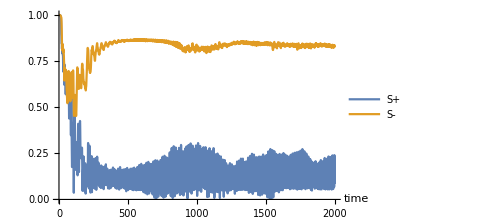
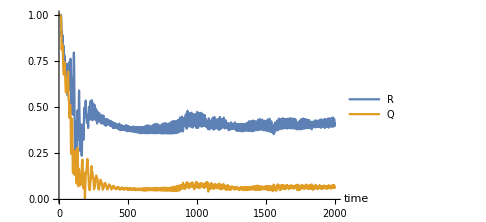
-Graphics- | -Graphics-

```mathematica
SeedRandom[0];
{dt,T,n1}={0.1,2000,1000};  (*dt = timestep, n = number of swarmalators*)
{J,k,β}={-0.5,1,0.1};      (*Change these parameters to experiment with the swarmalator system*)
{A,α}={1,π/2-β};
{z0,znew}={{Table[RandomReal[{0,0.1}],{i,1,n1}],Table[RandomReal[{0,0.1}],{i,1,n1}]},ConstantArray[0,{2,n1}]};
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps1,Wms1,Zs1,Ys1,ts}={{},{},{},{},{}};
While[t<NT,
znew=rk4New[z0,rhsNew,dt,J,k,A,α];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
{Y1,Z1}=findRs[znew];
AppendTo[Wps1,Wp1];AppendTo[Wms1,Wm1];AppendTo[Zs1,Z1];AppendTo[Ys1,Y1];AppendTo[ts,t*dt];
];
p1=ListPlot[{{ts,Wps1//Abs}ᵀ,{ts,Wms1//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"S+","S-"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p2=ListPlot[{{ts,Zs1//Abs}ᵀ,{ts,Ys1//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"R","Q"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
Grid[{{p1,p2}}]
```

#### Plot together

```mathematica
p1=ListPlot[{{ts,Zs//Abs}ᵀ,{ts,Zs1//Abs}ᵀ},AxesOrigin->{0,0},ImageSize->Medium,AxesLabel->{Style["time",15],Style["R",15]},Joined->True,ImageSize->Medium PlotRange->{0,1},PlotLabel->{"{dt,T,N,J,β} = "<>ToString[{dt,T,J,n1,β}]}];
p2=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms1//Abs}ᵀ},ImageSize->Medium,AxesOrigin->{0,0},AxesLabel->{Style["time",15],Style["S",15]},Joined->True,ImageSize->Medium PlotRange->{0,1},PlotLabel->{"{dt,T,N,J,β} = "<>ToString[{dt,T,J,n1,β}]}];
Grid[{{p1,p2}}]
```

-Graphics-

### Snake state: N = 2000 (check for convergence)

#### Start from R = 0 (uniform)

```mathematica
SeedRandom[0];
{dt,T,n1}={0.1,2000,2000};  (*dt = timestep, n = number of swarmalators*)
{J,k,β}={-0.5,1,0.1};      (*Change these parameters to experiment with the swarmalator system*)
{A,α}={1,π/2-β};
{z0,znew}={{Table[(2π)/n1 i//N,{i,1,n1}],Table[RandomReal[{0,2π}],{i,1,n1}]},ConstantArray[0,{2,n1}]};
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms,Zs,Ys,ts}={{},{},{},{},{}};
While[t<NT,
znew=rk4New[z0,rhsNew,dt,J,k,A,α];
z0=znew;t++;
{Wp,Wm}=findWs[znew];
{Y,Z}=findRs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Zs,Z];AppendTo[Ys,Y];AppendTo[ts,t*dt];
];
p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"S+","S-"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p2=ListPlot[{{ts,Zs//Abs}ᵀ,{ts,Ys//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"R","Q"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
Grid[{{p1,p2}}]
```

-Graphics- | -Graphics-

#### Start from R = 1 (sync)

```mathematica
SeedRandom[0];
{dt,T,n1}={0.1,2000,2000};  (*dt = timestep, n = number of swarmalators*)
{J,k,β}={-0.5,1,0.1};      (*Change these parameters to experiment with the swarmalator system*)
{A,α}={1,π/2-β};
{z0,znew}={{Table[RandomReal[{0,0.1}],{i,1,n1}],Table[RandomReal[{0,0.1}],{i,1,n1}]},ConstantArray[0,{2,n1}]};
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps1,Wms1,Zs1,Ys1,ts}={{},{},{},{},{}};
While[t<NT,
znew=rk4New[z0,rhsNew,dt,J,k,A,α];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
{Y1,Z1}=findRs[znew];
AppendTo[Wps1,Wp1];AppendTo[Wms1,Wm1];AppendTo[Zs1,Z1];AppendTo[Ys1,Y1];AppendTo[ts,t*dt];
];
p1=ListPlot[{{ts,Wps1//Abs}ᵀ,{ts,Wms1//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"S+","S-"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p2=ListPlot[{{ts,Zs1//Abs}ᵀ,{ts,Ys1//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"R","Q"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
Grid[{{p1,p2}}]
```

-Graphics- | -Graphics-

#### Plot together

```mathematica
p1=ListPlot[{{ts,Zs//Abs}ᵀ,{ts,Zs1//Abs}ᵀ},AxesOrigin->{0,0},ImageSize->Medium,AxesLabel->{Style["time",15],Style["R",15]},Joined->True,ImageSize->Medium PlotRange->{0,1},PlotLabel->{"{dt,T,N,J,β} = "<>ToString[{dt,T,J,n1,β}]}];
p2=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms1//Abs}ᵀ},ImageSize->Medium,AxesOrigin->{0,0},AxesLabel->{Style["time",15],Style["S",15]},Joined->True,ImageSize->Medium PlotRange->{0,1},PlotLabel->{"{dt,T,N,J,β} = "<>ToString[{dt,T,J,n1,β}]}];
Grid[{{p1,p2}}]
```

-Graphics- | -Graphics-

### Summary

1. I’m not sure what to think. It looks like the fluctuations somewhat die with large N. But not fully. Could it be that the state is weakly stable?
2. I should replot these figures using python’s odeint.

## Shy chimera

Seems to be quite delicate. If I make J, β small then its more stable

### (J, β )=(-0.025, 0.025)

#### N = 500

```mathematica
(*Simulate*)
SeedRandom[0];
{dt,T,n1}={0.25,1000,500};  (*dt = timestep, n = number of swarmalators*)
{J,k,β}={-0.025,1,0.025};      (*Change these parameters to experiment with the swarmalator system*)
{A,α}={1,π/2-β};
{z0,znew}={{Table[(2π)/n1 i//N,{i,1,n1}],Table[RandomReal[{0,2π}],{i,1,n1}]},ConstantArray[0,{2,n1}]};
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms,Zs,Ys,ts}={{},{},{},{},{}};
While[t<NT,
znew=rk4New[z0,rhsNew,dt,J,k,A,α];
z0=znew;t++;
{Wp,Wm}=findWs[znew];
{Y,Z}=findRs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Zs,Z];AppendTo[Ys,Y];AppendTo[ts,t*dt];
];

(*Plot*)
plotResults1D[znew]
p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"S+","S-"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p2=ListPlot[{{ts,Zs//Abs}ᵀ,{ts,Ys//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"R","Q"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
Grid[{{p1,p2}}]

p1=ListPlot[{{Wps//Re,Wps//Im}ᵀ},AxesOrigin->{0,0},AxesLabel->{"Re(W+)","Im(W+)"},LabelStyle->15,Joined->True,ImageSize->Medium,PlotRange->{{-1,1},{-1,1}}];
p2=ListPlot[{{Wms//Re,Wms//Im}ᵀ},AxesOrigin->{0,0},AxesLabel->{"Re(W-)","Im(W-)"},LabelStyle->15,Joined->True,ImageSize->Medium,PlotRange->{{-1,1},{-1,1}}];
p3=ListPlot[{{Zs//Re,Zs//Im}ᵀ},AxesOrigin->{0,0},AxesLabel->{"Re(Z)","Im(Z)"},LabelStyle->15,Joined->True,ImageSize->Medium,PlotRange->{{-1,1},{-1,1}}];
p4=ListPlot[{{Ys//Re,Ys//Im}ᵀ},AxesOrigin->{0,0},AxesLabel->{"Re(Y)","Im(Y)"},LabelStyle->15,Joined->True,ImageSize->Medium,PlotRange->{{-1,1},{-1,1}}];
Grid[{{p1,p2},{p3,p4}}]
```

$Aborted

-Graphics- | -Graphics- | -Graphics-

-Graphics- | -Graphics-

-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
ListPlot[{Arg[Wps],Arg[Wms]},Joined->True,PlotRange->{{2500,3000},Automatic}]
```

-Graphics-

#### N = 1000

```mathematica
(*Simulate*)
SeedRandom[0];
{dt,T,n1}={0.25,1000,1000};  (*dt = timestep, n = number of swarmalators*)
{J,k,β}={-0.025,1,0.025};      (*Change these parameters to experiment with the swarmalator system*)
{A,α}={1,π/2-β};
{z0,znew}={{Table[(2π)/n1 i//N,{i,1,n1}],Table[RandomReal[{0,2π}],{i,1,n1}]},ConstantArray[0,{2,n1}]};
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms,Zs,Ys,ts}={{},{},{},{},{}};
While[t<NT,
znew=rk4New[z0,rhsNew,dt,J,k,A,α];
z0=znew;t++;
{Wp,Wm}=findWs[znew];
{Y,Z}=findRs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Zs,Z];AppendTo[Ys,Y];AppendTo[ts,t*dt];
];

(*Plot*)
plotResults1D[znew]
p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"S+","S-"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p2=ListPlot[{{ts,Zs//Abs}ᵀ,{ts,Ys//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"R","Q"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
Grid[{{p1,p2}}]

p1=ListPlot[{{Wps//Re,Wps//Im}ᵀ},AxesOrigin->{0,0},AxesLabel->{"Re(W+)","Im(W+)"},LabelStyle->15,Joined->True,ImageSize->Medium,PlotRange->{{-1,1},{-1,1}}];
p2=ListPlot[{{Wms//Re,Wms//Im}ᵀ},AxesOrigin->{0,0},AxesLabel->{"Re(W-)","Im(W-)"},LabelStyle->15,Joined->True,ImageSize->Medium,PlotRange->{{-1,1},{-1,1}}];
p3=ListPlot[{{Zs//Re,Zs//Im}ᵀ},AxesOrigin->{0,0},AxesLabel->{"Re(Z)","Im(Z)"},LabelStyle->15,Joined->True,ImageSize->Medium,PlotRange->{{-1,1},{-1,1}}];
p4=ListPlot[{{Ys//Re,Ys//Im}ᵀ},AxesOrigin->{0,0},AxesLabel->{"Re(Y)","Im(Y)"},LabelStyle->15,Joined->True,ImageSize->Medium,PlotRange->{{-1,1},{-1,1}}];
Grid[{{p1,p2},{p3,p4}}]
```

$Aborted

-Graphics- | -Graphics- | -Graphics-

-Graphics- | -Graphics-

$Aborted

-Graphics- | -Graphics-
-Graphics- | -Graphics-

Looks like R and S = max(S+, S-) are anti-correlated.

```mathematica
p1=ListPlot[{{ts,Abs[Zs]-0.2}ᵀ,{ts,Wms//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"R - offset","S-"},Joined->True,ImageSize->Medium,PlotRange->{{250,500},{0,1}}]
```

-Graphics-

1. Yes.
2. Guess:  when R peaks the head of the chimera dominates, and when S peaks the tail dominates.

#### N = 2000

```mathematica
(*Simulate*)
SeedRandom[0];
{dt,T,n1}={0.25,500,2000};  (*dt = timestep, n = number of swarmalators*)
{J,k,β}={-0.025,1,0.025};      (*Change these parameters to experiment with the swarmalator system*)
{A,α}={1,π/2-β};
{z0,znew}={{Table[(2π)/n1 i//N,{i,1,n1}],Table[RandomReal[{0,2π}],{i,1,n1}]},ConstantArray[0,{2,n1}]};
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms,Zs,Ys,ts}={{},{},{},{},{}};
While[t<NT,
znew=rk4New[z0,rhsNew,dt,J,k,A,α];
z0=znew;t++;
{Wp,Wm}=findWs[znew];
{Y,Z}=findRs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Zs,Z];AppendTo[Ys,Y];AppendTo[ts,t*dt];
];

(*Plot*)
plotResults1D[znew]
p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"S+","S-"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p2=ListPlot[{{ts,Zs//Abs}ᵀ,{ts,Ys//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"R","Q"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
Grid[{{p1,p2}}]
```

-Graphics- | -Graphics- | -Graphics-

-Graphics- | -Graphics-

Looks like R and S = max(S+, S-) are anti-correlated. Huh. Maybe oscillations are a finite effect? Good news

```mathematica
(*Simulate*)
SeedRandom[0];
{dt,T,n1}={0.25,2000,2000};  (*dt = timestep, n = number of swarmalators*)
{J,k,β}={-0.025,1,0.025};      (*Change these parameters to experiment with the swarmalator system*)
{A,α}={1,π/2-β};
{z0,znew}={{Table[(2π)/n1 i//N,{i,1,n1}],Table[RandomReal[{0,2π}],{i,1,n1}]},ConstantArray[0,{2,n1}]};
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms,Zs,Ys,ts}={{},{},{},{},{}};
While[t<NT,
znew=rk4New[z0,rhsNew,dt,J,k,A,α];
z0=znew;t++;
{Wp,Wm}=findWs[znew];
{Y,Z}=findRs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Zs,Z];AppendTo[Ys,Y];AppendTo[ts,t*dt];
];

(*Plot*)
plotResults1D[znew]
p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"S+","S-"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p2=ListPlot[{{ts,Zs//Abs}ᵀ,{ts,Ys//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"R","Q"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
Grid[{{p1,p2}}]
```

-Graphics- | -Graphics- | -Graphics-

-Graphics- | -Graphics-

#### N = 5000

```mathematica
(*Simulate*)
SeedRandom[0];
{dt,T,n1}={0.25,1000,5000};  (*dt = timestep, n = number of swarmalators*)
{J,k,β}={-0.025,1,0.025};      (*Change these parameters to experiment with the swarmalator system*)
{A,α}={1,π/2-β};
{z0,znew}={{Table[(2π)/n1 i//N,{i,1,n1}],Table[RandomReal[{0,2π}],{i,1,n1}]},ConstantArray[0,{2,n1}]};
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms,Zs,Ys,ts}={{},{},{},{},{}};
While[t<NT,
znew=rk4New[z0,rhsNew,dt,J,k,A,α];
z0=znew;t++;
{Wp,Wm}=findWs[znew];
{Y,Z}=findRs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Zs,Z];AppendTo[Ys,Y];AppendTo[ts,t*dt];
];

(*Plot*)
plotResults1D[znew]
p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"S+","S-"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p2=ListPlot[{{ts,Zs//Abs}ᵀ,{ts,Ys//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"R","Q"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
Grid[{{p1,p2}}]
```

-Graphics- | -Graphics- | -Graphics-

-Graphics- | -Graphics-

Looks like R and S = max(S+, S-) are anti-correlated. Huh. Maybe oscillations are a finite effect? Good news

Run again for smaller T. Is it an X?

```mathematica
(*Simulate*)
SeedRandom[0];
{dt,T,n1}={0.1,1000,5000};  (*dt = timestep, n = number of swarmalators*)
{J,k,β}={-0.025,1,0.025};      (*Change these parameters to experiment with the swarmalator system*)
{A,α}={1,π/2-β};
{z0,znew}={{Table[(2π)/n1 i//N,{i,1,n1}],Table[RandomReal[{0,2π}],{i,1,n1}]},ConstantArray[0,{2,n1}]};
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms,Zs,Ys,ts}={{},{},{},{},{}};
While[t<NT,
znew=rk4New[z0,rhsNew,dt,J,k,A,α];
z0=znew;t++;
{Wp,Wm}=findWs[znew];
{Y,Z}=findRs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Zs,Z];AppendTo[Ys,Y];AppendTo[ts,t*dt];
];

(*Plot*)
plotResults1D[znew]
p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"S+","S-"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p2=ListPlot[{{ts,Zs//Abs}ᵀ,{ts,Ys//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"R","Q"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
Grid[{{p1,p2}}]
```

#### N = 10000

```mathematica
(*Simulate*)
SeedRandom[0];
{dt,T,n1}={0.25,750,10000};  (*dt = timestep, n = number of swarmalators*)
{J,k,β}={-0.025,1,0.025};      (*Change these parameters to experiment with the swarmalator system*)
{A,α}={1,π/2-β};
{z0,znew}={{Table[(2π)/n1 i//N,{i,1,n1}],Table[RandomReal[{0,2π}],{i,1,n1}]},ConstantArray[0,{2,n1}]};
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms,Zs,Ys,ts}={{},{},{},{},{}};
While[t<NT,
znew=rk4New[z0,rhsNew,dt,J,k,A,α];
z0=znew;t++;
{Wp,Wm}=findWs[znew];
{Y,Z}=findRs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Zs,Z];AppendTo[Ys,Y];AppendTo[ts,t*dt];
];

(*Plot*)
plotResults1D[znew]
p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"S+","S-"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p2=ListPlot[{{ts,Zs//Abs}ᵀ,{ts,Ys//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"R","Q"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
Grid[{{p1,p2}}]
```

$Aborted

-Graphics- | -Graphics- | -Graphics-

-Graphics- | -Graphics-

1. Looks like R and S = max(S+, S-) are anti-correlated. Huh. Maybe oscillations are a finite effect? Good news
2. This is just like the defect in the vinegar eels.

### All at once

#### dt = 0.25

```mathematica
(*Make data*)
ns={500,1000,5000,10000};
data=ParallelTable[(*Simulate*)
SeedRandom[0];
{dt,T}={0.25,1000};  (*dt = timestep, n = number of swarmalators*)
{J,k,β}={-0.025,1,0.025};      (*Change these parameters to experiment with the swarmalator system*)
{A,α}={1,π/2-β};
{z0,znew}={{Table[(2π)/n1 i//N,{i,1,n1}],Table[RandomReal[{0,2π}],{i,1,n1}]},ConstantArray[0,{2,n1}]};
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms,Zs,Ys,ts}={{},{},{},{},{}};
While[t<NT,
znew=rk4New[z0,rhsNew,dt,J,k,A,α];
z0=znew;t++;
{Wp,Wm}=findWs[znew];
{Y,Z}=findRs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Zs,Z];AppendTo[Ys,Y];AppendTo[ts,t*dt];
];
Print[ListPlot[data[[All,3]],AxesOrigin->{0,0},AxesLabel->{"t",Style["R",Italic]},LabelStyle->15,Joined->True,ImageSize->Medium]];
{Abs[Wps],Abs[Wms],Abs[Zs]},
{n1,ns}
];

(*Plot*)
p1=ListPlot[data[[All,1]],AxesOrigin->{0,0},AxesLabel->{"t","S_+"},LabelStyle->15,Joined->True,ImageSize->Medium,PlotLegends->{Table["N = "<>ToString[ns[[i]]],{i,1,Length[ns]}]}];
p2=ListPlot[data[[All,2]],AxesOrigin->{0,0},AxesLabel->{"t","S_-"},LabelStyle->15,Joined->True,ImageSize->Medium];
p3=ListPlot[data[[All,3]],AxesOrigin->{0,0},AxesLabel->{"t",Style["R",Italic]},LabelStyle->15,Joined->True,ImageSize->Medium];
Grid[{{p1,p2,p3}}]
```

#### dt = 0.05 (not set running yet)

```mathematica
(*Make data*)
ns={500,1000,5000,10000};
data=ParallelTable[(*Simulate*)
SeedRandom[0];
{dt,T}={0.05,1000};  (*dt = timestep, n = number of swarmalators*)
{J,k,β}={-0.025,1,0.025};      (*Change these parameters to experiment with the swarmalator system*)
{A,α}={1,π/2-β};
{z0,znew}={{Table[(2π)/n1 i//N,{i,1,n1}],Table[RandomReal[{0,2π}],{i,1,n1}]},ConstantArray[0,{2,n1}]};
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms,Zs,Ys,ts}={{},{},{},{},{}};
While[t<NT,
znew=rk4New[z0,rhsNew,dt,J,k,A,α];
z0=znew;t++;
{Wp,Wm}=findWs[znew];
{Y,Z}=findRs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Zs,Z];AppendTo[Ys,Y];AppendTo[ts,t*dt];
];
Print[ListPlot[data[[All,3]],AxesOrigin->{0,0},AxesLabel->{"t",Style["R",Italic]},LabelStyle->15,Joined->True,ImageSize->Medium]];
{Abs[Wps],Abs[Wms],Abs[Zs]},
{n1,ns}
];

(*Plot*)
p1=ListPlot[data[[All,1]],AxesOrigin->{0,0},AxesLabel->{"t","S_+"},LabelStyle->15,Joined->True,ImageSize->Medium,PlotLegends->{Table["N = "<>ToString[ns[[i]]],{i,1,Length[ns]}]}];
p2=ListPlot[data[[All,2]],AxesOrigin->{0,0},AxesLabel->{"t","S_-"},LabelStyle->15,Joined->True,ImageSize->Medium];
p3=ListPlot[data[[All,3]],AxesOrigin->{0,0},AxesLabel->{"t",Style["R",Italic]},LabelStyle->15,Joined->True,ImageSize->Medium];
Grid[{{p1,p2,p3}}]
```

## Order parameters S(J)

### Load data

#### All order parameters

```mathematica
SetDirectory[NotebookDirectory[]];
data=Table[
{β}={0.1};
{dt,T,n}={0.1,2000,500};
filename=ToString[StringForm["/Users/Kev/Documents/research/swarmalators/1D/on-ring/chimera/data/order_pars_dt_``_T_``_n_``_J_``_beta_``.mx",dt,T,n,J,β]];
{ts,Wp,Wm,Z,Y}=Import[filename];
cutoff=0.9*Length[Z];
{J,Mean[Abs[Z][[cutoff;;-1]]],Mean[Abs[Y][[cutoff;;-1]]],Mean[Abs[Wp][[cutoff;;-1]]],Mean[Abs[Wm][[cutoff;;-1]]]},
{J,0,-1.0,-0.05}
];
ListPlot[{data[[All,{1,2}]],data[[All,{1,3}]],data[[All,{1,4}]],data[[All,{1,5}]]},Joined->True,PlotLegends->{"R","Q","S+","S-"}]
```

-Graphics-

#### Just S

```mathematica
SetDirectory[NotebookDirectory[]];
data=Table[
{β}={0.1};
{dt,T,n}={0.1,2000,500};
filename=ToString[StringForm["/Users/Kev/Documents/research/swarmalators/1D/on-ring/chimera/data/order_pars_dt_``_T_``_n_``_J_``_beta_``.mx",dt,T,n,J,β]];
{ts,Wp,Wm,Z,Y}=Import[filename];
cutoff=0.9*Length[Z];
{J,Mean[Abs[Wp][[cutoff;;-1]]],Variance[Abs[Wp][[cutoff;;-1]]],Mean[Abs[Z][[cutoff;;-1]]],Variance[Abs[Z][[cutoff;;-1]]]},
{J,0,-1.0,-0.05}
];
Needs["ErrorBarPlots`"];
ErrorListPlot[{{data[[All,1]],data[[All,4]],data[[All,5]]}ᵀ,{data[[All,1]],data[[All,2]],data[[All,3]]}ᵀ},Joined->True,PlotLegends->{"R","S_+"}]
```

-Graphics-

#### Just R

```mathematica
data1=Table[
{β}={0.1};
{dt,T,n}={0.1,2000,500};
filename=ToString[StringForm["/Users/Kev/Documents/research/swarmalators/1D/on-ring/chimera/data/order_pars_dt_``_T_``_n_``_J_``_beta_``.mx",dt,T,n,J,β]];
{ts,Wp,Wm,Z,Y}=Import[filename];
cutoff=0.9*Length[Z];
{J,Mean[Abs[Z][[cutoff;;-1]]],Variance[Abs[Z][[cutoff;;-1]]]},
{J,0,-1.0,-0.05}
];
```

```mathematica
data2=Table[
{β}={0.1};
{dt,T,n}={0.1,2000,500};
filename=ToString[StringForm["/Users/Kev/Documents/research/swarmalators/1D/on-ring/chimera/data/order_pars_start_sync_dt_``_T_``_n_``_J_``_beta_``.mx",dt,T,n,J,β]];
{ts,Wp,Wm,Z,Y}=Import[filename];
cutoff=0.9*Length[Z];
{J,Mean[Abs[Z][[cutoff;;-1]]],Variance[Abs[Z][[cutoff;;-1]]]},
{J,0,-1.0,-0.05}
];
```

```mathematica
Needs["ErrorBarPlots`"];
ErrorListPlot[{{data1[[All,1]],data1[[All,2]],data1[[All,3]]}ᵀ,{data2[[All,1]],data2[[All,2]],data2[[All,3]]}ᵀ},Joined->True,PlotLegends->{"R","S_+"}]
```

-Graphics-

## Functions

```mathematica
rhs1D=Compile[{{z,_Real,2},{n,_Integer},{J,_Real},{k,_Real},{α,_Real}},
Module[{i,j,xji,yji,thetaji,inverseDistSq,inverseDist,xtemp,ytemp,thetatemp,rep,A,B,C,n1,vel=ConstantArray[0.0,{2,n}]},
For[i=1,i≤n,i++,
For[j=1,j≤n,j++,
If[j≠i,
xji=z[[1,j]]-z[[1,i]];
thetaji=z[[2,j]]-z[[2,i]];
xtemp=0 Sin[xji-α](1+J Cos[thetaji]);
thetatemp=k Sin[thetaji-α](1+J Cos[xji]);
vel[[1,i]]+=xtemp;
vel[[2,i]]+=thetatemp;
]
];
];
vel/N[n]
],
RuntimeAttributes->Listable,
Parallelization->True,
CompilationTarget->"C"
];

rhsNew=Compile[{{z,_Real,2},{n,_Integer},{J,_Real},{k,_Real},{A,_Real},{α,_Real}},
Module[{i,j,xji,yji,thetaji,inverseDistSq,inverseDist,xtemp,ytemp,thetatemp,rep,B,C,n1,vel=ConstantArray[0.0,{2,n}]},
For[i=1,i≤n,i++,
For[j=1,j≤n,j++,
If[j≠i,
xji=z[[1,j]]-z[[1,i]];
thetaji=z[[2,j]]-z[[2,i]];
xtemp=J Sin[xji-α](1+A Cos[thetaji]);
thetatemp=k Sin[thetaji-α](1+A Cos[xji]);
vel[[1,i]]+=xtemp;
vel[[2,i]]+=thetatemp;
]
];
];
vel/N[n]
],
RuntimeAttributes->Listable,
Parallelization->True,
CompilationTarget->"C"
];

rhsTwoalpha=Compile[{{z,_Real,2},{n,_Integer},{J,_Real},{k,_Real},{A,_Real},{α1,_Real},{α2,_Real}},
Module[{i,j,xji,yji,thetaji,inverseDistSq,inverseDist,xtemp,ytemp,thetatemp,rep,B,C,n1,vel=ConstantArray[0.0,{2,n}]},
For[i=1,i≤n,i++,
For[j=1,j≤n,j++,
If[j≠i,
xji=z[[1,j]]-z[[1,i]];
thetaji=z[[2,j]]-z[[2,i]];
xtemp=J Sin[xji-α1](1+A Cos[thetaji]);
thetatemp=k Sin[thetaji-α2](1+A Cos[xji]);
vel[[1,i]]+=xtemp;
vel[[2,i]]+=thetatemp;
]
];
];
vel/N[n]
],
RuntimeAttributes->Listable,
Parallelization->True,
CompilationTarget->"C"
];

findWs[z_]:=Block[{Wp,Wm,i,numOsc},
{Wp,Wm}={0,0};
numOsc=Length[z[[1]]];
For[i=1,i≤numOsc,i++,
Wp+=Exp[ⅈ (z[[1,i]]-z[[2,i]])];
Wm+=Exp[ⅈ (z[[1,i]]+z[[2,i]])];
];
Return[{Wp/numOsc,Wm/numOsc}]
];

findRs[z_]:=Block[{Z,Y,i,numOsc},
{Z,Y}={0,0};
numOsc=Length[z[[1]]];
For[i=1,i≤numOsc,i++,
Y+=Exp[ⅈ (z[[1,i]])];
Z+=Exp[ⅈ (z[[2,i]])];
];
Return[{Y/numOsc,Z/numOsc}]
]

plotResults1D[z_]:=Block[{colors,Wp,Wm,Rx,Rtheta,p1,p2,p3},
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[z[[2,All]],2π]-1)/(2π)+380);
{Wp,Wm}=findWs[z];
{Rx,Rtheta}=findRs[z];
p1=Graphics[{

(*Swarmalators*)
PointSize[0.02],Point[{Cos[z[[1,All]]],Sin[z[[1,All]]]}ᵀ,VertexColors->colors],

(*Order parameters*)
PointSize[0.05],
Cyan,Point[{Rx//Re,Rx//Im}],Black,Text["Y",{Rx//Re,Rx//Im}],
Magenta,Point[{Rtheta//Re,Rtheta//Im}],Black,Text["Z",{Rtheta//Re,Rtheta//Im}],
Green,Point[{Wp//Re,Wp//Im}],Black,Text["W_+",{Wp//Re,Wp//Im}],
Green,Point[{Wm//Re,Wm//Im}],Black,Text["W_-",{Wm//Re,Wm//Im}],

(*Domain*)
Black,Circle[{0,0},1]
},
PlotRange->{{-1.25,1.25},{-1.25,1.25}},Axes->True,Ticks->None,AspectRatio->1,AxesLabel->{"x","y"},LabelStyle->20,ImageSize->Medium];
p2=ListPlot[{Mod[z[[1,All]],2π],Mod[z[[2,All]],2π]}ᵀ,PlotRange->{{0,2π},{0,2π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["θ",15]}];
p3=ListPlot[{Mod[z[[1,All]]+z[[2,All]],2π],Mod[z[[1,All]]-z[[2,All]],2π]}ᵀ,PlotRange->{{0π,2π},{0π,2π}},ImageSize->Medium,AxesLabel->{Style["ξ",15],Style["η",15]}];
Return[Grid[{{p1,p2,p3}}]
]
];

plotResults1DB[z_]:=Block[{colors},
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[z[[2,All]],2π]-1)/(2π)+380);
Return[ListPlot[{z[[1,All]],z[[2,All]]}ᵀ,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium]]
];

eulerStep1D[z_,F_,dt_,J_,k_,α_]:=Block[{znew,n,i,j,vel},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
vel=F[z,n,J,k,α];
For[j=1,j≤2,j++,
For[i=1,i≤n,i++,
znew[[j,i]]=z[[j,i]]+dt*vel[[j,i]]
];
];
Return[znew]
];

rk4[z_,F_,dt_,J_,k_,α_]:=Block[{znew,n,i,j,k1,k2,k3,k4},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
k1=F[z,n,J,k,α];
k2=F[z+dt/2 k1,n,J,k,α];
k3=F[z+dt/2 k2,n,J,k,α];
k4=F[z+dt k3,n,J,k,α];
Return[z+dt/6(k1+2k2+2k3+k4)]
];


rk4New[z_,F_,dt_,J_,k_,A_,α_]:=Block[{znew,n,i,j,k1,k2,k3,k4},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
k1=F[z,n,J,k,A,α];
k2=F[z+dt/2 k1,n,J,k,A,α];
k3=F[z+dt/2 k2,n,J,k,A,α];
k4=F[z+dt k3,n,J,k,A,α];
Return[z+dt/6(k1+2k2+2k3+k4)]
];


rk42alpha[z_,F_,dt_,J_,k_,A_,α1_,α2_]:=Block[{znew,n,i,j,k1,k2,k3,k4},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
k1=F[z,n,J,k,A,α1,α2];
k2=F[z+dt/2 k1,n,J,k,A,α1,α2];
k3=F[z+dt/2 k2,n,J,k,A,α1,α2];
k4=F[z+dt k3,n,J,k,A,α1,α2];
Return[z+dt/6(k1+2k2+2k3+k4)]
];

mod[θ_]:=Mod[θ,2π]-π;
```